```mathematica
"Tent Map"
f[x_] := Piecewise[{
{2 * a * x, 0 ≤ x ≤ 1/2},
{2 * a * (1 - x), 1/ 2 ≤ x ≤ 1}
}]
f2[x_]:= Piecewise[{
{4*a^2*x, 0 ≤ x ≤ 1/(4*a)},
{2*a - 4*a^2 + 4*a^2*x, 1/(4 * a) ≤ x ≤ 1/(2*a)}
}]
```

Tent Map

```mathematica
f[x]
```

Piecewise[{{2 a x, 0≤x≤1/2}, {2 a (1-x), 1/2≤x≤1}, {0, True}}]

```mathematica
" a) Para mostrar que el mapa es no invertible alcanza con mostrar que para los valores de x -> 0 y 1 el mapa arroja el mismo valor, por lo que su pre imagen no es única, demostrandose su no invertibilidad";
" b) Reemplazamos a = 3/8 y a = 5/8, determinamos los puntos fijos y su estabilidad." ;
```

```mathematica
fa1[x_] := f[x] /. {a -> 3/8}
fa2[x_]:=  f[x] /. {a -> 5/8}
fa1root1 = fa1[x][[1]][[1]][[1]] -x ==0
fa1root2 = fa1[x][[1]][[2]][[1]] -x ==0
fa2root1 = fa2[x][[1]][[1]][[1]] -x ==0
fa2root2 = fa2[x][[1]][[2]][[1]] -x ==0
fpa11 = Reduce[{fa1root1}, {x}][[2]];
fpa12 = Reduce[{fa1root2}, {x}][[2]];
fpa1roots = {fpa11, fpa12}
fpa21 = Reduce[{fa2root1}, {x}][[2]];
fpa22 = Reduce[{fa2root2}, {x}][[2]];
fpa2roots = {fpa21, fpa22}
```

-x/4==0

(3 (1-x))/4-x==0

x/4==0

(5 (1-x))/4-x==0

{0,3/7}

{0,5/9}

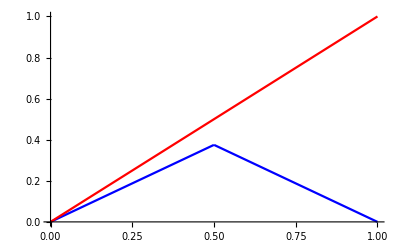

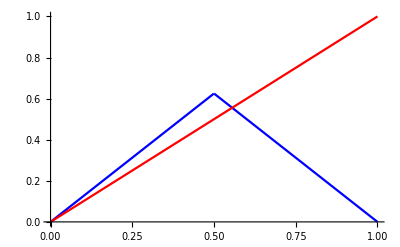

```mathematica
plot1 =Plot[fa1[x], {x, 0, 1}, PlotStyle->Blue, PlotRange->{0, 1}];
plot2 = Plot[x, {x, 0, 1}, PlotStyle->Red, PlotRange->{0, 1}];
Show[plot1, plot2]
plot1 =Plot[fa2[x], {x, 0, 1}, PlotStyle->Blue, PlotRange->{0, 1}];
plot2 = Plot[x, {x, 0, 1}, PlotStyle->Red, PlotRange->{0, 1}];
Show[plot1, plot2]
```

```mathematica
"Vemos que x = 0 es el único punto fijo de período 1, puesto que 3/7 cae fuera del intervalo donde está definido el mapa.
Su estabilidad se verifica calculando los autovalores de la matriz jacobiana A del lado derecho.";

fa11 = fa1[x][[1]][[1]][[1]];
fa21 = fa2[x][[1]][[1]][[1]];
fa22 = fa2[x][[1]][[2]][[1]];
A11 = D[fa11, x]
"El punto fijo tiene un autovalor de 3/4, está dentro del circulo unidad, y como el único autovalor, este punto fijo es hiperbólico. Además como su valor absoluto es menor a la unidad es un sumidero."
A21 = D[fa21, x]
"Este punto fijo tiene autovalor distinto de 1 en valor absoluto, por lo que es hiperbólico, pero aquí es mayor a uno, por lo que es una fuente."
A22 = D[fa22, x]
"Por último este punto fijo tiene autovalor distinto a 1 en valor absoluto, por lo que es hiperbólico, también mayor a uno por lo que es una fuente."
```

3/4

El punto fijo tiene un autovalor de 3/4, está dentro del circulo unidad, y como el único autovalor, este punto fijo es hiperbólico. Además como su valor absoluto es menor a la unidad es un sumidero.

5/4

Este punto fijo tiene autovalor distinto de 1 en valor absoluto, por lo que es hiperbólico, pero aquí es mayor a uno, por lo que es una fuente.

-5/4

Por último este punto fijo tiene autovalor distinto a 1 en valor absoluto, por lo que es hiperbólico, también mayor a uno por lo que es una fuente.

```mathematica
"Ahora analizamos el mapa de periodo 2."
```

Ahora analizamos el mapa de periodo 2.

```mathematica
f2part1= f[x][[1]][[1]][[1]] /. {x -> f[x][[1]][[1]][[1]]};
f2part1= FullSimplify[f2part1]
f2part2= f[x][[1]][[2]][[1]] /. {x -> f[x][[1]][[2]][[1]]};
f2part2= Expand[f2part2]
```

4 a^2 x

2 a-4 a^2+4 a^2 x

```mathematica
fb1 = f2[x] /. {a -> 3/8}
fb2 =  f2[x] /. {a -> 5/8}
```

Piecewise[{{(9 x)/16, 0≤x≤2/3}, {3/16+(9 x)/16, 2/3≤x≤4/3}, {0, True}}]

Piecewise[{{(25 x)/16, 0≤x≤2/5}, {-5/16+(25 x)/16, 2/5≤x≤4/5}, {0, True}}]

```mathematica
fb1root1 = fb1[[1]][[1]][[1]] -x ==0
fb1root2 = fb1[[1]][[2]][[1]] -x ==0
fb2root1 = fb2[[1]][[1]][[1]] -x ==0
fb2root2 = fb2[[1]][[2]][[1]] -x ==0
fpb11 = Reduce[{fb1root1}, {x}][[2]];
fpb12 = Reduce[{fb1root2}, {x}][[2]];
fpb1roots = {fpb11, fpb12}
fpb21 = Reduce[{fb2root1}, {x}][[2]];
fpb22 = Reduce[{fb2root2}, {x}][[2]];
fpb2roots = {fpb21, fpb22}
```

-(7 x)/16==0

3/16-(7 x)/16==0

(9 x)/16==0

-5/16+(9 x)/16==0

{0,3/7}

{0,5/9}

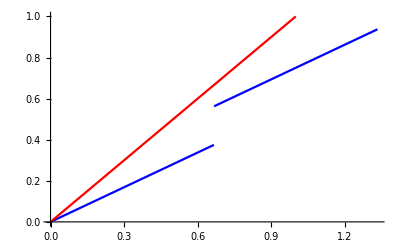

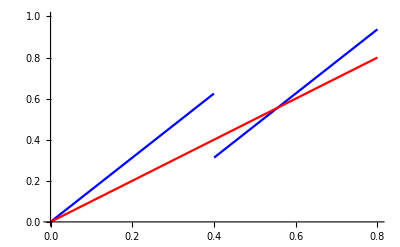

```mathematica
plot1 =Plot[fb1, {x, 0, 4/3}, PlotStyle->Blue, PlotRange->{0, 1}];
plot2 = Plot[x, {x, 0,  4/3}, PlotStyle->Red, PlotRange->{0, 1}];
Show[plot1, plot2]
plot1 =Plot[fb2, {x, 0, 4/5}, PlotStyle->Blue, PlotRange->{0, 1}];
plot2 = Plot[x, {x, 0, 4/5}, PlotStyle->Red, PlotRange->{0, 1}];
Show[plot1, plot2]
```

```mathematica
"Vemos que las raíces son las mismas, y si ahora evaluamos sus autovalores, obviando la raiz 3/7 puesto que no está en el intervalo del mapa donde está definido.";
fb11 = fb1[[1]][[1]][[1]]
A11 = D[fb11, x] /. {x -> fpb1roots[[1]]}
fb21 = fb2[[1]][[1]][[1]]
A21 = D[fb21, x] /. {x -> fpb2roots[[1]]}
fb22 = fb2[[1]][[2]][[1]]
A22 = D[fb22, x] /. {x -> fpb2roots[[2]]}
```

(9 x)/16

9/16

(25 x)/16

25/16

-5/16+(25 x)/16

25/16

```mathematica
"El punto fijo en 0 para el primer a es de valor absoluto menor a 1 por lo que es un sumidero, el punto fijo en 0 para el segundo a es una fuente y también lo es el punto fijo en 5/9."
```

El punto fijo en 0 para el primer a es de valor absoluto menor a 1 por lo que es un sumidero, el punto fijo en 0 para el segundo a es una fuente y también lo es el punto fijo en 5/9.

```mathematica
f2[x_]:= Simplify[f[f[x]] /. {a -> 5/8}]
```

```mathematica
f2[x]
```

Piecewise[{{-25/16 (-1+x), 3/5≤x≤1}, {(25 x)/16, 0≤x≤2/5}, {-5/16 (-4+5 x), 2/5<x≤1/2}, {5/16 (-1+5 x), 1/2<x<3/5}, {0, True}}]

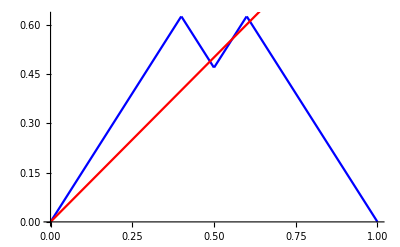

```mathematica
plot1 = Plot[f2[x], {x, 0, 1}, PlotStyle->Blue];
plot2 = Plot[x, {x, 0, 1}, PlotStyle->Red];
Show[plot1, plot2]
```

```mathematica
f2part11 = f2[x][[1]][[1]][[1]] - x == 0
f2part12 = f2[x][[1]][[1]][[2]]
f2root1 = Reduce[{f2part11, f2part12}, {x}]
f2part21 = f2[x][[1]][[2]][[1]] - x == 0
f2part22 = f2[x][[1]][[2]][[2]]
f2root2 = Reduce[{f2part21, f2part22}, {x}]
f2part31 = f2[x][[1]][[3]][[1]] - x == 0
f2part32 = f2[x][[1]][[3]][[2]]
f2root3 = Reduce[{f2part31, f2part32}, {x}]
f2part41 = f2[x][[1]][[4]][[1]] - x == 0
f2part42 = f2[x][[1]][[4]][[2]]
f2root4 = Reduce[{f2part41, f2part42}, {x}]
```

-25/16 (-1+x)-x==0

3/5≤x≤1

x==25/41

(9 x)/16==0

0≤x≤2/5

x==0

-x-5/16 (-4+5 x)==0

2/5<x≤1/2

x==20/41

-x+5/16 (-1+5 x)==0

1/2<x<3/5

x==5/9

```mathematica
"Tenemos 4 puntos fijos, ahora analizaremos el jacobiano en los mismos.";
```

```mathematica
D[f2part11[[1]], x]
D[f2part21[[1]], x]
D[f2part31[[1]], x]
D[f2part41[[1]], x]
```

-41/16

9/16

-41/16

9/16

```mathematica
"Los valores de los Jacobianos no dependen de los ceros, podemos inmediatamente definir sus estabilidades.
Los autovalores del 1er y 3er tramo son mayoes a uno en valor absoluto, tratandose de puntos fijos hiperbólicos y son fuentes. Los autovalores del cuarto y segundo cero son menores a 1 en valor absoluto, son ambos hiperbólicos y sumideros.";
```

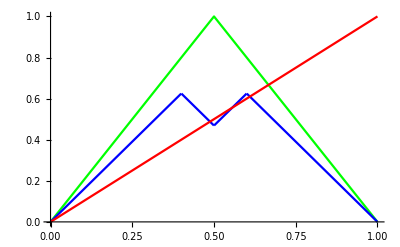

```mathematica
plot0 = Plot[f[x][[1]], {x, 0, 1}, PlotStyle->Green];
plot1 = Plot[f2[x], {x, 0, 1}, PlotStyle->Blue];
plot2 = Plot[x, {x, 0, 1}, PlotStyle->Red];
Show[plot0, plot1, plot2]
```

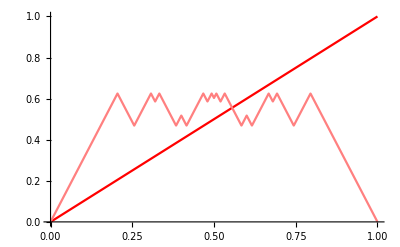

```mathematica
plot0 = Plot[x, {x, 0, 1}, PlotStyle->Red];
plot1 = Plot[f[x][[1]], {x, 0, 1}, PlotStyle->Green];
plot2 = Plot[f2[x], {x, 0, 1}, PlotStyle->Blue];
plot3 = Plot[f3[x], {x, 0, 1}, PlotStyle->Orange];
plot4 = Plot[f4[x], {x, 0, 1}, PlotStyle->Purple];
plot5 = Plot[f5[x], {x, 0, 1}, PlotStyle->Pink];
Show[plot0,plot5]
```

```mathematica
f3[x_]:= f2[f[x]]
```

```mathematica
f4[x_]:= f3[f[x]]
f5[x_] := f4[f[x]]
```

```mathematica
f3[x]
```

Piecewise[{{-125/64 (-1+x), 17/25≤x≤1}, {(125 x)/64, 0≤x≤8/25}, {-25/64 (-4+5 x), 12/25≤x≤1/2}, {25/64 (-1+5 x), 1/2<x≤13/25}, {-5/64 (-21+25 x), 13/25<x<3/5}, {5/4-(125 x)/64, 8/25<x≤2/5}, {5/64 (-9+25 x), 3/5≤x<17/25}, {5/64 (-4+25 x), 2/5<x<12/25}, {0, True}}]

```mathematica
Reduce[f3[x][[1]][[5]][[1]] - x ==0, x]
```

x==5/9

```mathematica
N[Reduce[f3[x][[1]][[5]][[1]] - x ==0, x][[2]]]
N[f3[x][[1]][[5]][[2]]]
```

0.555556

0.52<x<0.6

```mathematica
f5[x]
```

Piecewise[{{-(3125 (-1+x))/1024, 497/625≤x≤1}, {(3125 x)/1024, 0≤x≤128/625}, {-(25 (-109+125 x))/1024, 417/625≤x<17/25}, {-(25 (-89+125 x))/1024, 317/625≤x≤13/25}, {-(25 (-84+125 x))/1024, 292/625≤x<12/25}, {-(25 (-64+125 x))/1024, 192/625≤x≤8/25}, {(25 (-61+125 x))/1024, 17/25≤x≤433/625}, {(25 (-41+125 x))/1024, 13/25<x≤333/625}, {(25 (-36+125 x))/1024, 12/25≤x≤308/625}, {(25 (-16+125 x))/1024, 8/25<x≤208/625}, {-(5 (-561+625 x))/1024, 433/625<x<93/125}, {-(5 (-481+625 x))/1024, 3/5≤x≤77/125}, {-(5 (-461+625 x))/1024, 333/625<x<73/125}, {-(5 (-436+625 x))/1024, 308/625<x≤1/2}, {(5 (-369+625 x))/1024, 93/125≤x<497/625}, {-(5 (-356+625 x))/1024, 2/5<x≤52/125}, {-(5 (-336+625 x))/1024, 208/625<x<48/125}, {(5 (-289+625 x))/1024, 77/125<x<417/625}, {(5 (-269+625 x))/1024, 73/125≤x<3/5}, {5/4-(3125 x)/1024, 128/625<x≤32/125}, {(5 (-189+625 x))/1024, 1/2<x<317/625}, {(5 (-164+625 x))/1024, 52/125<x<292/625}, {(5 (-144+625 x))/1024, 48/125≤x≤2/5}, {(5 (-64+625 x))/1024, 32/125<x<192/625}, {0, True}}]

```mathematica
N[Reduce[f5[x][[1]][[16]][[1]] - x ==0][[2]]]
N[f5[x][[1]][[16]][[2]]]
```

0.429019

0.4<x≤0.416